# Limit Cycle Analysis

## Goal of this analysis: demonstrate how the changing shape of limit cycles (and to a lesser extent, the location of fixed points) translates to the “net change” measure that has proven to be useful for predicting the endpoints of an HP mechanism

```mathematica
<<"/Users/LJSbo/Documents/Wolfram Mathematica/Dynamica.m"
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

## Dynamical System Definition

```mathematica
σ[x_]=1/(1+ⅇ^-x);
```

```mathematica
CTRNN3y=
DynamicalSystem[
{(-y1+w11 σ[y1+θ1]+w21 σ[y2+θ2]+w31 σ[y3+θ3]+S)/τ1,(-y2+w12 σ[y1+θ1]+w22 σ[y2+θ2]+w32 σ[y3+θ3]+S)/τ2,(-y3+w13 σ[y1+θ1]+w23 σ[y2+θ2]+w33 σ[y3+θ3]+S)/τ3},
{{y1,-16,16},{y2,-16,16},{y3,-16,16}},
{{w11,-16,16},{w12,-16,16},{w13,-16,16},{w21,-16,16},{w22,-16,16},{w23,-16,16},{w31,-16,16},{w32,-16,16},{w33,-16,16},{θ1,-16,16},{θ2,-16,16},{θ3,-16,16},{τ1,0.5,10},{τ2,0.5,10},{τ3,0.5,10},{S,-16,16}}];
```

#### Enter Evolved Parameters

```mathematica
CTRNN3y=CTRNN3y/.{w11->-0.304589,w12-> 3.63678,w13->-15.722,w21->-7.71592,w22->7.83063,w23->14.7452,w31->-10.4152,w32->-15.456,w33->3.74962,θ1->4.04929,θ2->-0.450597,θ3->-4.63354,τ1->1.38354,τ2-> 1.66468,τ3-> 1.65868,S->0};
```

#### HP parameters

```mathematica
HPLB1 = 0.17125;
HPUB1 = 0.17125 + 0.0261298;
HPLB3 = 0.355329;
HPUB3 = 0.355329;
```

```mathematica
LB1plane = {Opacity[.75,LightBlue],InfinitePlane[{{HPLB1,0,0.5},{HPLB1,1,1},{HPLB1,.5,0}}]};
UB1plane = {Opacity[.75,LightPink],InfinitePlane[{{HPUB1,0,0.5},{HPUB1,1,1},{HPUB1,.5,0}}]};
LB1planebif = {Opacity[.75,LightBlue],InfinitePlane[{{0,HPLB1,0.5},{1,HPLB1,1},{.5,HPLB1,0}}]};
UB1planebif = {Opacity[.75,LightPink],InfinitePlane[{{0,HPUB1,0.5},{1,HPUB1,1},{.5,HPUB1,0}}]};
LB3plane = {Opacity[.75,LightPurple],InfinitePlane[{{0,.5,HPLB3},{1,1,HPLB3},{.5,0,HPLB3}}]};
```

```mathematica
Show[Graphics3D[LB1plane],Graphics3D[UB1plane],Graphics3D[LB3plane]]
```

-Graphics3D-

#### Substitute in Value for visualized slice of plane

```mathematica
CTRNN3y = CTRNN3y /.{θ3->-2.5};
```

```mathematica
With[{ε=10^-9},
CTRNN3o=
TransformDynamicalSystem[CTRNN3y,{{o1,ε,1-ε},{o2,ε,1-ε},{o3,ε,1-ε}},{σ[y1+θ1],σ[y2+θ2],σ[y3+θ3]}]];
```

#### Display Limit Cycle and Threshold Planes

```mathematica
DisplayTrajectories[CTRNN3o,{{0.09051847148981729,0.000053913874608498984,0.3837324371617314}},11.5]
  Last[First[$Trajectories]]
```

-Graphics3D-

{0.0838448,0.0000485841,0.398026}

```mathematica
LCblue=FindLimitCycle[CTRNN3o,  Last[First[$Trajectories]] ,11.5]
```

LimitCycle[Stable,11.5494,{0.0838449,0.0000485869,0.398026}]

```mathematica
Show[DisplayPhasePortrait[CTRNN3o,LimitSets->{LCblue},Tries->100],Graphics3D[LB3plane]]
```

-Graphics3D-

theoretically, this limit cycle is too far below the plane, bias will be moved up

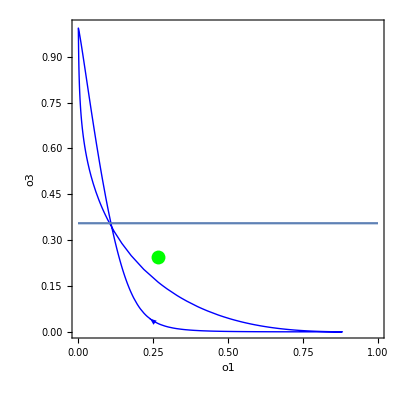

```mathematica
Show[DisplayPhasePortrait[CTRNN3o,LimitSets->{LCblue},StateVariables->{o1,o3},Tries->100],Plot[HPLB3,{x,0,1}]]
```

```mathematica
CTRNN3y = CTRNN3y/.{θ3->-10};
```

```mathematica
With[{ε=10^-9},
CTRNN3o=
TransformDynamicalSystem[CTRNN3y,{{o1,ε,1-ε},{o2,ε,1-ε},{o3,ε,1-ε}},{σ[y1+θ1],σ[y2+θ2],σ[y3+θ3]}]];
```

```mathematica
DisplayTrajectories[CTRNN3o,{{0.07091345368180887,0.03965350553006576,0.024762070673664018}},6.2]
  Last[First[$Trajectories]]
```

-Graphics3D-

{0.0290676,0.028906,0.0555047}

```mathematica
LCred=FindLimitCycle[CTRNN3o,  Last[First[$Trajectories]] ,6.3]
```

LimitCycle[Stable,6.39797,{0.0290774,0.0289278,0.0555149}]

```mathematica
Show[DisplayPhasePortrait[CTRNN3o,LimitSets->{LCred},Tries->100],Graphics3D[LB3plane]]
```

-Graphics3D-

theoretically, this cycle is too far above the plane, bias will be moved down

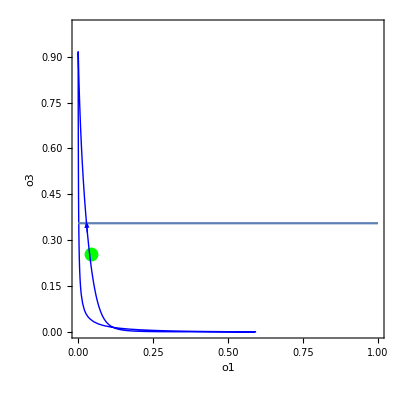

```mathematica
Show[DisplayPhasePortrait[CTRNN3o, LimitSets->{LCred}, StateVariables->{o1,o3}],Plot[HPLB3,{x,0,1}]]
```

```mathematica
CTRNN3y = CTRNN3y/.{θ3->-5.1};
```

```mathematica
With[{ε=10^-9},
CTRNN3o=
TransformDynamicalSystem[CTRNN3y,{{o1,ε,1-ε},{o2,ε,1-ε},{o3,ε,1-ε}},{σ[y1+θ1],σ[y2+θ2],σ[y3+θ3]}]];
```

```mathematica
DisplayTrajectories[CTRNN3o,{{0.10221193670183916,0.0010925853412138652,0.1432025700959155}},7.5]
  Last[First[$Trajectories]]
```

-Graphics3D-

{0.0571793,0.000484556,0.199388}

```mathematica
LCwhite=FindLimitCycle[CTRNN3o,  Last[First[$Trajectories]] ,7.5]
```

LimitCycle[Stable,7.75326,{0.0570609,0.000478868,0.199329}]

```mathematica
Show[DisplayPhasePortrait[CTRNN3o,LimitSets->{LCwhite},Tries->100],Graphics3D[LB3plane],Graphics3D[UB1plane],Graphics3D[LB1plane]]
```

-Graphics3D-

theoretically, this cycle is balanced with respect to both planes (net change zero. It is interesting that the unstable fixed point is sandwiched in the acceptable range for N1, but not so for N3

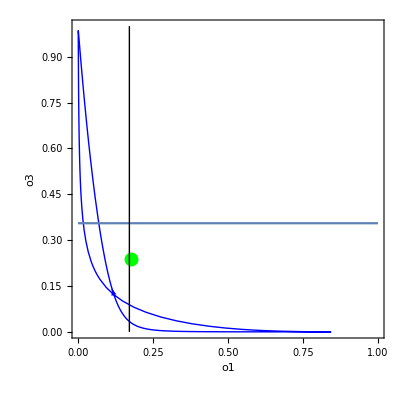

```mathematica
Show[DisplayPhasePortrait[CTRNN3o, LimitSets->{LCwhite}, StateVariables->{o1,o3}],Plot[HPLB3,{x,0,1}],Graphics[Line[{{HPLB1,0},{HPLB1,1}}]]]
```

#### “Blue” vs “Red” limit cycles in N1

```mathematica
CTRNN3y = CTRNN3y/.{θ1->0,θ3->-4.63354};
```

```mathematica
With[{ε=10^-9},
CTRNN3o=
TransformDynamicalSystem[CTRNN3y,{{o1,ε,1-ε},{o2,ε,1-ε},{o3,ε,1-ε}},{σ[y1+θ1],σ[y2+θ2],σ[y3+θ3]}]];
```

```mathematica
DisplayTrajectories[CTRNN3o,{{0.07091345368180887,0.03965350553006576,0.024762070673664018}},6.2]
  Last[First[$Trajectories]]
```

-Graphics3D-

{0.0721113,0.0464261,0.0411845}

```mathematica
LCredb1=FindLimitCycle[CTRNN3o,  Last[First[$Trajectories]] ,6.3]
```

LimitCycle[Stable,5.86712,{0.0689041,0.0534005,0.046003}]

```mathematica
Show[DisplayPhasePortrait[CTRNN3o,LimitSets->{LCredb1},Tries->100],Graphics3D[LB1plane]]
```

-Graphics3D-

obviously, this cycle is too far left of the plane, bias will be moved up

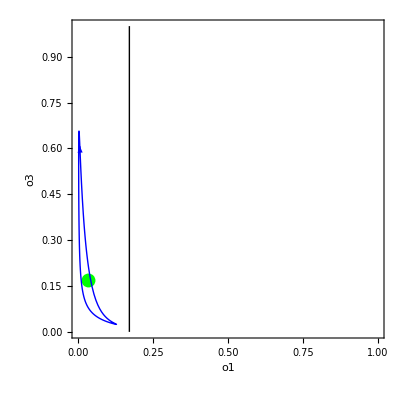

```mathematica
Show[DisplayPhasePortrait[CTRNN3o, LimitSets->{LCredb1}, StateVariables->{o1,o3}],Graphics[Line[{{HPLB1,0},{HPLB1,1}}]]]
```

```mathematica
CTRNN3y = CTRNN3y/.{θ1->9,θ3->-4.63354};
```

```mathematica
With[{ε=10^-9},
CTRNN3o=
TransformDynamicalSystem[CTRNN3y,{{o1,ε,1-ε},{o2,ε,1-ε},{o3,ε,1-ε}},{σ[y1+θ1],σ[y2+θ2],σ[y3+θ3]}]];
```

```mathematica
DisplayTrajectories[CTRNN3o,{{0.1790037928175193,0.9962453091166501,0.7999494014001577}},12.5]
  Last[First[$Trajectories]]
```

-Graphics3D-

{0.0456072,0.97134,0.968619}

```mathematica
LCblueb1=FindLimitCycle[CTRNN3o,  Last[First[$Trajectories]] ,12.4]
```

LimitCycle[Stable,12.2486,{0.045601,0.971351,0.968625}]

```mathematica
Show[DisplayPhasePortrait[CTRNN3o,LimitSets->{LCblueb1},Tries->100],Graphics3D[UB1plane],Graphics3D[LB1plane]]
```

-Graphics3D-

obviously, this cycle too far right of the plane, bias will be moved down

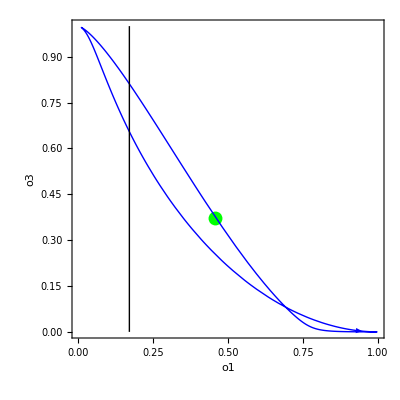

```mathematica
Show[DisplayPhasePortrait[CTRNN3o, LimitSets->{LCblueb1}, StateVariables->{o1,o3}],Graphics[Line[{{HPLB1,0},{HPLB1,1}}]]]
```

```mathematica
CTRNN3y=CTRNN3y/.{w11->-0.304589,w12-> 3.63678,w13->-15.722,w21->-7.71592,w22->7.83063,w23->14.7452,w31->-10.4152,w32->-15.456,w33->3.74962,θ1->4.04929,θ2->-0.450597,θ3->-4.63354,τ1->1.38354,τ2-> 1.66468,τ3-> 1.65868,S->0};
```

```mathematica
With[{ε=10^-9},
CTRNN3o=
TransformDynamicalSystem[CTRNN3y,{{o1,ε,1-ε},{o2,ε,1-ε},{o3,ε,1-ε}},{σ[y1+θ1],σ[y2+θ2],σ[y3+θ3]}]];
```

```mathematica
LCB = FollowLimitCycleBranch[LCwhite,θ1,MaxStepSize->0.01];
```

```mathematica
(*Make Plot*)
Show[
DisplayBifurcationDiagram[CTRNN3o,θ1,StateVariables->{o1,o3},MaxSteps->Infinity,LimitCycleBranches->{LCB},PlotRange->{{-5,15},{0,1},{0,1}},AxesStyle->Directive[Black,12]],Graphics3D[LB1planebif],Graphics3D[LB3plane]]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

NullSpace::mindet: Input matrix contains an indeterminate entry.

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {o1,o2,o3,θ1}={0,0.160899,0.15922,-16}

-Graphics3D-

The difference between HP33 and HP37 is that HP37 is too permissive of the limit cycles on the right side of this diagram (don’t realize they’re too high)